# 3RRR Parallel Planar Manipulator

## Dynamics

```mathematica
q={θ1[t],θ2[t],θ3[t],ϕ1[t],ϕ2[t],ϕ3[t],x[t],y[t],α[t]};
param={a->0.110,b->0.168 *2 *Sqrt[3],l->0.1525,r->0.22875,ρ->2700,g->9.807};
mparam={ml->ρ 0.00009872913,mr->ρ 0.000222700,mt->ρ 0.000257200,Il->0.0009182,Ir->0.00425,It->0.004635}/.param;
aparam={θ1[t]->-0.8130256652456614,θ2[t]->1.3341010762167809,θ3[t]->-2.682001449053732,ϕ1[t]->1.1187319342794553,ϕ2[t]->-2.9066592029379716,ϕ3[t]->-0.8803243261319863,α[t]->0,x[t]->0.300,y[t]->0.150}
```

{θ1[t]→-0.813026,θ2[t]→1.3341,θ3[t]→-2.682,ϕ1[t]→1.11873,ϕ2[t]→-2.90666,ϕ3[t]→-0.880324,α[t]→0,x[t]→0.3,y[t]→0.15}

```mathematica
dq=D[q,t];
pl1= {l Cos[θ1[t]],l Sin[θ1[t]]};
dl1= {l Cos[θ1[t]]+ r Cos[ϕ1[t]],l Sin[θ1[t]]+ r Sin[ϕ1[t]]};
pl2={b+ l Cos[θ2[t]],l Sin[θ2[t]]};
dl2={b+ l Cos[θ2[t]]+ r Cos[ϕ2[t]],l Sin[θ2[t]]+ r Sin[ϕ2[t]]};
pl3={b/2+ l Cos[θ3[t]],Sqrt[3]b/2+ l Sin[θ3[t]]};
dl3={b/2+ l Cos[θ3[t]]+ r Cos[ϕ3[t]],Sqrt[3]b/2+ l Sin[θ3[t]]+ r Sin[ϕ3[t]]};
```

```mathematica
(*Branch_1*)
cm11={(1/2) l Cos[θ1[t]],(1/2) l Sin[θ1[t]]};
cm12={ l Cos[θ1[t]]+(r/2) Cos[ϕ1[t]], l Sin[θ1[t]]+(r/2) Sin[ϕ1[t]]};
```

```mathematica
(*Branch_2*)
cm21={b+(1/2) l Cos[θ2[t]],(1/2) l Sin[θ2[t]]};
cm22={ b+l Cos[θ2[t]]+(r/2) Cos[ϕ2[t]], l Sin[θ2[t]]+(r/2) Sin[ϕ2[t]]};
```

```mathematica
(*Branch_3*)
cm31={b/2+(1/2) l Cos[θ3[t]],Sqrt[3] b/2 +(1/2) l Sin[θ3[t]]};
cm32={ b/2+l Cos[θ3[t]]+(r/2 )Cos[ϕ3[t]],Sqrt[3] b/2+ l Sin[θ3[t]]+(r/2) Sin[ϕ3[t]]};
```

```mathematica
(*End_effector*)
cm4={x[t],y[t]};
(*Velocities*)
v11=Simplify[D[cm11,t]];
v12=Simplify[D[cm12,t]];
v21=Simplify[D[cm21,t]];
v22=Simplify[D[cm22,t]];
v31=Simplify[D[cm31,t]];
v32=Simplify[D[cm32,t]];
v4=Simplify[D[cm4,t]];
```

```mathematica
(*Kinetic_Energies*)
ke11=(1/2 )ml (v11.v11)+(1/2 ) Il (dq[[1]]^2);
ke21=(1/2 )ml (v21.v21)+(1/2 ) Il (dq[[2]]^2);
ke31=(1/2 )ml (v31.v31)+(1/2 ) Il (dq[[3]]^2);
ke12=(1/2 )mr(v11.v11)+(1/2 ) Ir (dq[[4]]^2);
ke22=(1/2 )mr (v21.v21)+(1/2 ) Ir (dq[[5]]^2);
ke32=(1/2 )mr (v31.v31)+(1/2 ) Ir (dq[[6]]^2);
ke4=(1/2 )mt (v4.v4)+(1/2 ) It (dq[[9]]^2);
tke=Simplify[Expand[ ke11+ke21+ke31+ke12+ke22+ke32+ke4]]
```

1/8 (4 mt x'[t]^2+4 mt y'[t]^2+4 It α'[t]^2+4 Il θ1'[t]^2+l^2 ml θ1'[t]^2+l^2 mr θ1'[t]^2+4 Il θ2'[t]^2+l^2 ml θ2'[t]^2+l^2 mr θ2'[t]^2+4 Il θ3'[t]^2+l^2 ml θ3'[t]^2+l^2 mr θ3'[t]^2+4 Ir ϕ1'[t]^2+4 Ir ϕ2'[t]^2+4 Ir ϕ3'[t]^2)

```mathematica
(*potential_Energies*)
pe11=ml g cm11[[2]];
pe21=ml g cm21[[2]];
pe31=ml g cm31[[2]];
pe12=mr g cm12[[2]];
pe22=mr g cm22[[2]];
pe32=mr g cm32[[2]];
pe4=mt g cm4[[2]];
tpe=Simplify[Expand[pe11+pe21+pe31+pe12+pe22+pe32+pe4]]
```

1/2 g (√3 b ml+√3 b mr+l (ml+2 mr) Sin[θ1[t]]+l ml Sin[θ2[t]]+2 l mr Sin[θ2[t]]+l ml Sin[θ3[t]]+2 l mr Sin[θ3[t]]+mr r Sin[ϕ1[t]]+mr r Sin[ϕ2[t]]+mr r Sin[ϕ3[t]]+2 mt y[t])

```mathematica
L=Simplify[ Expand[ tke-tpe]]/.param/.mparam
```

1/8 (-34.3167-8.78884 Sin[θ1[t]]-8.78884 Sin[θ2[t]]-8.78884 Sin[θ3[t]]-5.39562 Sin[ϕ1[t]]-5.39562 Sin[ϕ2[t]]-5.39562 Sin[ϕ3[t]]-54.483 y[t]+2.77776 x'[t]^2+2.77776 y'[t]^2+0.01854 α'[t]^2+0.0238559 θ1'[t]^2+0.0238559 θ2'[t]^2+0.0238559 θ3'[t]^2+0.017 ϕ1'[t]^2+0.017 ϕ2'[t]^2+0.017 ϕ3'[t]^2)

```mathematica
eq1=Simplify[Expand[D[D[L,dq[[1]]],t]-D[L,q[[1]]]]]
eq2=Simplify[Expand[D[D[L,dq[[2]]],t]-D[L,q[[2]]]]]
eq3=Simplify[Expand[D[D[L,dq[[3]]],t]-D[L,q[[3]]]]]
eq4=Simplify[Expand[D[D[L,dq[[4]]],t]-D[L,q[[4]]]]]
eq5=Simplify[Expand[D[D[L,dq[[5]]],t]-D[L,q[[5]]]]]
eq6=Simplify[Expand[D[D[L,dq[[6]]],t]-D[L,q[[6]]]]]
eq7=Simplify[Expand[D[D[L,dq[[7]]],t]-D[L,q[[7]]]]]
eq8=Simplify[Expand[D[D[L,dq[[8]]],t]-D[L,q[[8]]]]]
eq9=Simplify[Expand[D[D[L,dq[[9]]],t]-D[L,q[[9]]]]]
```

1.09861 Cos[θ1[t]]+0.00596398 θ1''[t]

1.09861 Cos[θ2[t]]+0.00596398 θ2''[t]

1.09861 Cos[θ3[t]]+0.00596398 θ3''[t]

0.674452 Cos[ϕ1[t]]+0.00425 ϕ1''[t]

0.674452 Cos[ϕ2[t]]+0.00425 ϕ2''[t]

0.674452 Cos[ϕ3[t]]+0.00425 ϕ3''[t]

0.69444 x''[t]

6.81037+0.69444 y''[t]

0.004635 α''[t]

```mathematica
M=Simplify[{{Coefficient[eq1,θ1''[t]],Coefficient[eq1,θ2''[t]],Coefficient[eq1,θ3''[t]],Coefficient[eq1,ϕ1''[t]],Coefficient[eq1,ϕ2''[t]],Coefficient[eq1,ϕ3''[t]],Coefficient[eq1,x''[t]],Coefficient[eq1,y''[t]],Coefficient[eq1,α''[t]]},
{Coefficient[eq2,θ1''[t]],Coefficient[eq2,θ2''[t]],Coefficient[eq2,θ3''[t]],Coefficient[eq2,ϕ1''[t]],Coefficient[eq2,ϕ2''[t]],Coefficient[eq2,ϕ3''[t]],Coefficient[eq2,x''[t]],Coefficient[eq2,y''[t]],Coefficient[eq2,α''[t]]},
{Coefficient[eq3,θ1''[t]],Coefficient[eq3,θ2''[t]],Coefficient[eq3,θ3''[t]],Coefficient[eq3,ϕ1''[t]],Coefficient[eq3,ϕ2''[t]],Coefficient[eq3,ϕ3''[t]],Coefficient[eq3,x''[t]],Coefficient[eq3,y''[t]],Coefficient[eq3,α''[t]]},
{Coefficient[eq4,θ1''[t]],Coefficient[eq4,θ2''[t]],Coefficient[eq4,θ3''[t]],Coefficient[eq4,ϕ1''[t]],Coefficient[eq4,ϕ2''[t]],Coefficient[eq4,ϕ3''[t]],Coefficient[eq4,x''[t]],Coefficient[eq4,y''[t]],Coefficient[eq4,α''[t]]},
{Coefficient[eq5,θ1''[t]],Coefficient[eq5,θ2''[t]],Coefficient[eq5,θ3''[t]],Coefficient[eq5,ϕ1''[t]],Coefficient[eq5,ϕ2''[t]],Coefficient[eq5,ϕ3''[t]],Coefficient[eq5,x''[t]],Coefficient[eq5,y''[t]],Coefficient[eq5,α''[t]]},
{Coefficient[eq6,θ1''[t]],Coefficient[eq6,θ2''[t]],Coefficient[eq6,θ3''[t]],Coefficient[eq6,ϕ1''[t]],Coefficient[eq6,ϕ2''[t]],Coefficient[eq6,ϕ3''[t]],Coefficient[eq6,x''[t]],Coefficient[eq6,y''[t]],Coefficient[eq6,α''[t]]},
{Coefficient[eq7,θ1''[t]],Coefficient[eq7,θ2''[t]],Coefficient[eq7,θ3''[t]],Coefficient[eq7,ϕ1''[t]],Coefficient[eq7,ϕ2''[t]],Coefficient[eq7,ϕ3''[t]],Coefficient[eq7,x''[t]],Coefficient[eq7,y''[t]],Coefficient[eq7,α''[t]]},
{Coefficient[eq8,θ1''[t]],Coefficient[eq8,θ2''[t]],Coefficient[eq8,θ3''[t]],Coefficient[eq8,ϕ1''[t]],Coefficient[eq8,ϕ2''[t]],Coefficient[eq8,ϕ3''[t]],Coefficient[eq8,x''[t]],Coefficient[eq8,y''[t]],Coefficient[eq8,α''[t]]},
{Coefficient[eq9,θ1''[t]],Coefficient[eq9,θ2''[t]],Coefficient[eq9,θ3''[t]],Coefficient[eq9,ϕ1''[t]],Coefficient[eq9,ϕ2''[t]],Coefficient[eq9,ϕ3''[t]],Coefficient[eq9,x''[t]],Coefficient[eq9,y''[t]],Coefficient[eq9,α''[t]]}}]
```

{{0.00596398,0,0,0,0,0,0,0,0},{0,0.00596398,0,0,0,0,0,0,0},{0,0,0.00596398,0,0,0,0,0,0},{0,0,0,0.00425,0,0,0,0,0},{0,0,0,0,0.00425,0,0,0,0},{0,0,0,0,0,0.00425,0,0,0},{0,0,0,0,0,0,0.69444,0,0},{0,0,0,0,0,0,0,0.69444,0},{0,0,0,0,0,0,0,0,0.004635}}

```mathematica
MatrixForm[M]
```

(0.00596398 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.00596398 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.00596398 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.00425 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.00425 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.00425 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.69444 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.69444 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.004635)

```mathematica
Cor=ConstantArray[0,{9,9}];
```

```mathematica
For[ii=1,ii<=9,ii++,
For[jj=1,jj<=9,jj++,
For[kk=1,kk<=9,kk++,
Cor[[ii,jj]]+=0.5(D[M[[ii,jj]],q[[kk]]]+D[M[[ii,kk]],q[[jj]]]-D[M[[kk,jj]],q[[ii]]])*dq[[kk]];
];
];
];
```

```mathematica
check=D[M,t]-2*Cor;
```

```mathematica
G= D[tpe,{q}]/.param/.mparam
```

{1.09861 Cos[θ1[t]],1.09861 Cos[θ2[t]],1.09861 Cos[θ3[t]],0.674452 Cos[ϕ1[t]],0.674452 Cos[ϕ2[t]],0.674452 Cos[ϕ3[t]],0,6.81037,0}

```mathematica
(* Constraints;  Postion of CM of End effector;*)
(* W.r.t  1;*)
η1= l Cos[θ1[t]]+ r Cos[ϕ1[t]]+ a Cos[(π/6)+ α[t]]-x[t];
η2= l Sin[θ1[t]]+ r Sin[ϕ1[t]]+ a Sin[(π/6)+ α[t]]-y[t];
(* w.r.t 2;*)
η3=b+ l Cos[θ2[t]]+ r Cos[ϕ2[t]]+ a Cos[(5π/6)+ α[t]]-x[t];
η4= l Sin[θ2[t]]+ r Sin[ϕ2[t]]+ a Sin[(5π/6)+ α[t]]-y[t];
(* w.r.t 3;*)
η5=b/2+ l Cos[θ3[t]]+ r Cos[ϕ3[t]]+ a Cos[(3π/2)+ α[t]]-x[t];
η6=Sqrt[3]b/2+ l Sin[θ3[t]]+ r Sin[ϕ3[t]]+ a Sin[(3π/2)+ α[t]]-y[t];

η={η1,η2,η3,η4,η5,η6};
Jηq=D[η,{q}];
MatrixForm[Jηq];
```

```mathematica
Jηdq=D[Jηq,t];
```

```mathematica
A =Jηq.Inverse[M].Transpose[Jηq] ;
```

```mathematica
qnc= {0,0,0,0,0,0,0,0,0};
f= qnc - Cor.dq - G;
MatrixForm[f];
```

```mathematica
λ = -(Inverse[A].(Jηdq.dq+Jηq.Inverse[M].f));
```

```mathematica
ddq = Inverse[M].f - Inverse[M].Transpose[Jηq].Inverse[A].(Jηdq.dq+Jηq.Inverse[M].f);
```

```mathematica
qdata= ddq /.param/.mparam;
```

```mathematica
qdata[[1]]/.aparam/.{θ1'[t]->0,θ2'[t]->0,θ3'[t]->0,ϕ1'[t]->0,ϕ2'[t]->0,ϕ3'[t]->0,α'[t]->0,x'[t]->0,y'[t]->0};
```

```mathematica
qdata[[2]]/.aparam/.{θ1'[t]->0,θ2'[t]->0,θ3'[t]->0,ϕ1'[t]->0,ϕ2'[t]->0,ϕ3'[t]->0,α'[t]->0,x'[t]->0,y'[t]->0};
```

```mathematica
qdata[[3]]/.aparam/.{θ1'[t]->0,θ2'[t]->0,θ3'[t]->0,ϕ1'[t]->0,ϕ2'[t]->0,ϕ3'[t]->0,α'[t]->0,x'[t]->0,y'[t]->0};
```

```mathematica
qdata[[4]]/.aparam/.{θ1'[t]->0,θ2'[t]->0,θ3'[t]->0,ϕ1'[t]->0,ϕ2'[t]->0,ϕ3'[t]->0,α'[t]->0,x'[t]->0,y'[t]->0};
```

```mathematica
qdata[[5]]/.aparam/.{θ1'[t]->0,θ2'[t]->0,θ3'[t]->0,ϕ1'[t]->0,ϕ2'[t]->0,ϕ3'[t]->0,α'[t]->0,x'[t]->0,y'[t]->0};
```

```mathematica
qdata[[6]]/.aparam/.{θ1'[t]->0,θ2'[t]->0,θ3'[t]->0,ϕ1'[t]->0,ϕ2'[t]->0,ϕ3'[t]->0,α'[t]->0,x'[t]->0,y'[t]->0};
```

```mathematica
qdata[[7]]/.aparam/.{θ1'[t]->0,θ2'[t]->0,θ3'[t]->0,ϕ1'[t]->0,ϕ2'[t]->0,ϕ3'[t]->0,α'[t]->0,x'[t]->0,y'[t]->0};
```

```mathematica
qdata[[8]]/.aparam/.{θ1'[t]->0,θ2'[t]->0,θ3'[t]->0,ϕ1'[t]->0,ϕ2'[t]->0,ϕ3'[t]->0,α'[t]->0,x'[t]->0,y'[t]->0};
```

```mathematica
qdata[[9]]/.aparam/.{θ1'[t]->0,θ2'[t]->0,θ3'[t]->0,ϕ1'[t]->0,ϕ2'[t]->0,ϕ3'[t]->0,α'[t]->0,x'[t]->0,y'[t]->0};
```

```mathematica
qdatachop=Chop[qdata];
```

```mathematica
tf=10;
s1=NDSolve[{{θ1''[t],θ2''[t],θ3''[t],ϕ1''[t],ϕ2''[t],ϕ3''[t],x''[t],y''[t],α''[t]}-{qdata[[1]],qdata[[2]],qdata[[3]],qdata[[4]],qdata[[5]],qdata[[6]],qdata[[7]],qdata[[8]],qdata[[9]]}=={0,0,0,0,0,0,0,0,0},θ1[0]==-0.8157688508294761,θ2[0]==1.2786262491302358,θ3[0]==-2.910163957861006,ϕ1[0]==1.0756486485384968,ϕ2[0]==-3.1131415592588962,ϕ3[0]==-1.0187464547457152,x[0]==0.290984535,y[0]==0.168,α[0]==π/12,θ1'[0]==0,θ2'[0]==0,θ3'[0]==0,ϕ1'[0]==0,ϕ2'[0]==0,ϕ3'[0]==0,x'[0]==0,y'[0]==0,α'[0]==0},{θ1,θ2,θ3,ϕ1,ϕ2,ϕ3,x,y,α},{t,0,tf},Method->{"EquationSimplification"->"Residual"}]
```

{{θ1→InterpolatingFunction[…],θ2→InterpolatingFunction[…],θ3→InterpolatingFunction[…],ϕ1→InterpolatingFunction[…],ϕ2→InterpolatingFunction[…],ϕ3→InterpolatingFunction[…],x→InterpolatingFunction[…],y→InterpolatingFunction[…],α→InterpolatingFunction[…]}}

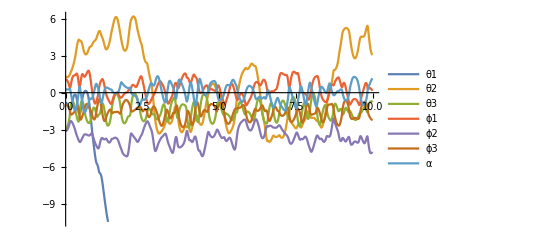

```mathematica
Plot[Evaluate[{θ1[t],θ2[t],θ3[t],ϕ1[t],ϕ2[t],ϕ3[t],α[t]}/. s1],{t,0,tf},PlotStyle->Automatic,PlotLegends->{θ1,θ2,θ3,ϕ1,ϕ2,ϕ3,α}]
```

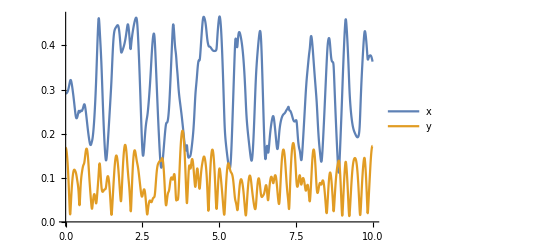

```mathematica
Plot[Evaluate[{x[t],y[t]}/. s1],{t,0,tf},PlotStyle->Automatic,PlotLegends->{x,y}]
```

```mathematica
timestep=0.01;
tf=10;
(*Create a list of the solution at different times with a step of'timestep' starting from 0 till the final simulation time*)

solList=Inner[Rule,Flatten[{q,dq,tim}],#,List]&/@Table[Flatten[{q,dq,t}/.s1[[1]]],{t,0,tf,timestep}];
```

```mathematica
(*Time axis for plot*)
time=tim/.solList;
```

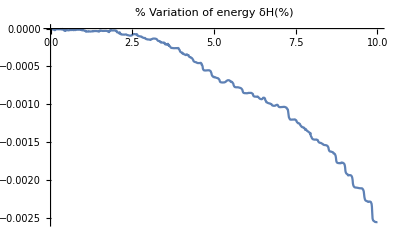

```mathematica
(*Energy Check*)
H=(tke+tpe)/.param/.mparam /.solList;
δH=100*((H/H[[1]])-Table[1,{Length[solList]}]);
ListPlot[Inner[List,time,δH,List],Joined->True,PlotLabel->"% Variation of energy δH(%)"]
```

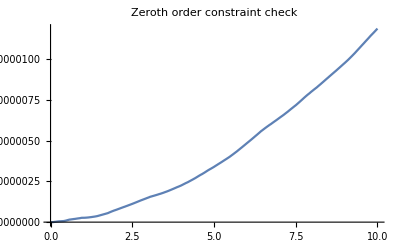

```mathematica
ηList=Table[Norm[(η)/.solList[[i]]/.param],{i,Length[solList]}];
ListPlot[Inner[List,time,ηList,List],Joined->True,PlotLabel->"Zeroth order constraint check"]
```

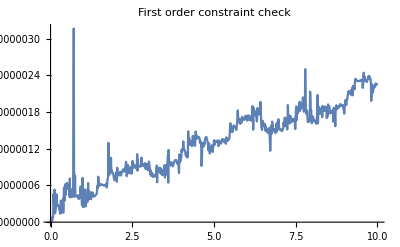

```mathematica
JηList=Table[Norm[Jηq.dq/.solList[[i]]/.param],{i,Length[solList]}];
ListPlot[Inner[List,time,JηList,List],Joined->True,PlotLabel->"First order constraint check"]
```

## Trajectory planning

```mathematica
figure[{l_,r_,a_,b_},param_]:=Module[{line1,line2,line3,circle1,circle2,circle3,circle4},
       line1=Graphics[{Black,Line[{{0,0},{b,0}}]}]/.param;
line2=Graphics[{Black,Line[{{b,0},{b/2,(Sqrt[3]*b)/2}}]}]/.param;
line3=Graphics[{Black,Line[{{b/2,(Sqrt[3]*b)/2},{0,0}}]}]/.param;
circle1=Graphics[{Red,Circle[{0,0},l+r+a]}]/.param;
circle2=Graphics[{Red,Circle[{b,0},l+r+a]}]/.param;
circle3=Graphics[{Red,Circle[{b/2,(Sqrt[3]*b)/2},l+r+a]}]/.param;
circle4=Graphics[{Blue,Circle[{b/2,b/(2 *Sqrt[3])},0.120 ]}]/.param;
Show[{line1,line2,line3,circle1,circle2,circle3,circle4}]
];
```

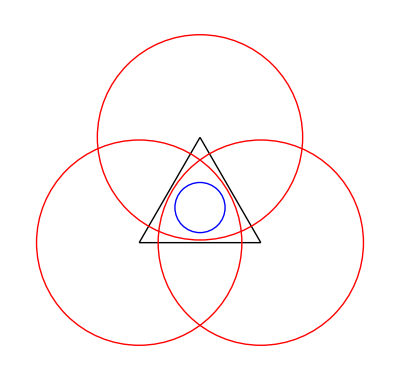

```mathematica
figure[{l,r,a,b},param]
```

```mathematica
(*Determining cubic trajectory coefficients*)
initconds={ϕ0->0,ϕf->2π,dϕ0->0,dϕf->0};
traj=a0+a1 t+a2 t^2+a3 t^3;
dtraj=D[traj,t];
eq1traj=(traj/.{t->0})-ϕ0;
eq2traj=(traj/.{t->tf})-ϕf;
eq3traj=(dtraj/.{t->0})-dϕ0;
eq4traj=(dtraj/.{t->tf})-dϕf;
solcoeff=Solve[{eq1traj,eq2traj,eq3traj,eq4traj}==0,{a0,a1,a2,a3}][[1]];
trajf=traj/.solcoeff/.initconds;
dtrajf=D[trajf,t];
```

```mathematica
(*Determining position velocity and acceleration on the circular trajectory*)
n=0.01;
(*pathparams={xc->b/2,yc->b/(2 *Sqrt[3]),a->120,b->120,tF->TF}/.param;
xpos=(xc+a Cos[ϕ])/.{ϕ->trajf}/.pathparams;
ypos=(yc+b Sin[ϕ])/.{ϕ->trajf}/.pathparams;
alphapos=0;
pos={xpos,ypos,alphapos};
pathvel=D[pos,t];
pathacc=D[pathvel,t];*)
pathparams={xc->b/2,yc->b/(2 *Sqrt[3]),rc->0.120,tfn->10}/.param;
xpos=(xc+rc Cos[ϕ])/.{ϕ->trajf}/.pathparams;
ypos=(yc+rc Sin[ϕ])/.{ϕ->trajf}/.pathparams;
αpos=0;
pos={xpos,ypos,αpos};
pathvel=D[pos,t];
pathacc=D[pathvel,t];
```

```mathematica
(*Discretizing position velocity and acceleration on the circular trajectory in task space for Inverse Dynamics*)

posv=Table[pos,{t,0,tf,n}];
velv=Table[pathvel,{t,0,tf,n}];
accv=Table[pathacc,{t,0,tf,n}];
```

## Inverse Dynamics

```mathematica
IK[{l_,r_,a_,b_,θ1_,θ2_,θ3_,ϕ1_,ϕ2_,ϕ3_,x_,y_,α_}]:=Module[{ik1,ik2,ik3,ik4,ik5,ik6,ik12,ik22,ik13,ik23,ik32,ik42,ik52,ik62,ik33,ik43,ik53,ik63,t,subs,subs2,subs3,solth1,solth2,solth3,angle111,angle112,angle121,angle122,angle211,angle212,angle221,angle222,ϕ1a,ϕ2a,ϕ3a,ϕ1b,ϕ2b,ϕ3b,branch1,branch2,branch3,branch4,branch5,branch6,branch7,branch8},

ik1= l Cos[θ1]+ r Cos[ϕ1]+ a Cos[(π/6)+ α]-x;
ik2= l Sin[θ1]+ r Sin[ϕ1]+ a Sin[(π/6)+ α]-y;
ik12=b+ l Cos[θ2]+ r Cos[ϕ2]+ a Cos[(5π/6)+ α]-x;
ik22= l Sin[θ2]+ r Sin[ϕ2]+ a Sin[(5π/6)+ α]-y;
ik13=b/2+ l Cos[θ3]+ r Cos[ϕ3]+ a Cos[(3π/2)+ α]-x;
ik23=Sqrt[3]b/2+ l Sin[θ3]+ r Sin[ϕ3]+ a Sin[(3π/2)+ α]-y;
ik3=Solve[{ik1,ik2}=={0,0},{Cos[ϕ1],Sin[ϕ1]}][[1]];
ik4=Simplify[Numerator[Together[(Cos[ϕ1]^2 + Sin[ϕ1]^2  -1)/.ik3]]];
(*Print[ik4]*)
subs={Cos[θ1]->(1-t^2)/(1+t^2),Sin[θ1]->(2 t /(1+t^2))};
ik5=Collect[Numerator[Together[TrigExpand[ik4]/.subs]],t];
ik6=Solve[ik5==0,t];
solth1={θ1->2*ArcTan[t/.ik6[[1]]],θ1->2*ArcTan[t/.ik6[[2]]]};
ik32=Solve[{ik12,ik22}=={0,0},{Cos[ϕ2],Sin[ϕ2]}][[1]];
ik42=Simplify[Numerator[Together[(Cos[ϕ2]^2 + Sin[ϕ2]^2  -1)/.ik32]]];
subs2={Cos[θ2]->(1-t^2)/(1+t^2),Sin[θ2]->(2 t /(1+t^2))};
ik52=Collect[Numerator[Together[TrigExpand[ik42]/.subs2]],t];
ik62=Simplify[Solve[ik52==0,t]];
solth2={θ2->2*ArcTan[t/.ik62[[1]]],θ2->2*ArcTan[t/.ik62[[2]]]};
ik33=Solve[{ik13,ik23}=={0,0},{Cos[ϕ3],Sin[ϕ3]}][[1]];
ik43=Numerator[Together[(Cos[ϕ3]^2 + Sin[ϕ3]^2  -1)/.ik33]];
subs3={Cos[θ3]->(1-t^2)/(1+t^2),Sin[θ3]->(2 t /(1+t^2))};
ik53=Collect[Numerator[Together[ik43/.subs3]],t];
ik63=Simplify[Solve[ik53==0,t]];
solth3={θ3->2*ArcTan[t/.ik63[[1]]],θ3->2*ArcTan[t/.ik63[[2]]]};
angle111={solth1[[1]],solth2[[1]],solth3[[1]]};
angle112={solth1[[1]],solth2[[1]],solth3[[2]]};
angle121={solth1[[1]],solth2[[2]],solth3[[1]]};
angle122={solth1[[1]],solth2[[2]],solth3[[2]]};
angle211={solth1[[2]],solth2[[1]],solth3[[1]]};
angle212={solth1[[2]],solth2[[1]],solth3[[2]]};
angle221={solth1[[2]],solth2[[2]],solth3[[1]]};
angle222={solth1[[2]],solth2[[2]],solth3[[2]]};
ϕ1a={ϕ1-> ArcTan[Cos[ϕ1]/.ik3,Sin[ϕ1]/.ik3]/.angle111};
ϕ1b= {ϕ1->ArcTan[Cos[ϕ1]/.ik3,Sin[ϕ1]/.ik3]/.angle211};
ϕ2a= {ϕ2->ArcTan[Cos[ϕ2]/.ik32,Sin[ϕ2]/.ik32]/.angle111};
ϕ2b= {ϕ2->ArcTan[Cos[ϕ2]/.ik32,Sin[ϕ2]/.ik32]/.angle222};
ϕ3a= {ϕ3->ArcTan[Cos[ϕ3]/.ik33,Sin[ϕ3]/.ik33]/.angle121};
ϕ3b= {ϕ3->ArcTan[Cos[ϕ3]/.ik33,Sin[ϕ3]/.ik33]/.angle222};branch1=Join[angle111,ϕ1a,ϕ2a,ϕ3a];
branch2=Join[angle112,ϕ1a,ϕ2a,ϕ3b];
branch3=Join[angle121,ϕ1a,ϕ2b,ϕ3a];
branch4=Join[angle122,ϕ1a,ϕ2b,ϕ3b];
branch5=Join[angle211,ϕ1b,ϕ2a,ϕ3a];
branch6=Join[angle212,ϕ1b,ϕ2a,ϕ3b];
branch7=Join[angle221,ϕ1b,ϕ2b,ϕ3a];
branch8=Join[angle222,ϕ1b,ϕ2b,ϕ3b];
Return[branch1];
]
```

```mathematica
solbr1=IK[{l,r,a,b,θ1,θ2,θ3,ϕ1,ϕ2,ϕ3,x,y,α}];
```

```mathematica
dθ1=D[((θ1/.solbr1)/.{x->x[t],y->y[t],α->α[t]}),t];
dθ2=D[((θ2/.solbr1)/.{x->x[t],y->y[t],α->α[t]}),t];
dθ3=D[((θ3/.solbr1)/.{x->x[t],y->y[t],α->α[t]}),t];
dϕ1=D[((ϕ1/.solbr1)/.{x->x[t],y->y[t],α->α[t]}),t];
dϕ2=D[((ϕ2/.solbr1)/.{x->x[t],y->y[t],α->α[t]}),t];
dϕ3=D[((ϕ3/.solbr1)/.{x->x[t],y->y[t],α->α[t]}),t];
```

```mathematica
ddθ1=D[dθ1,t];
ddθ2=D[dθ1,t];
ddθ3=D[dθ1,t];
ddϕ1=D[dϕ1,t];
ddϕ2=D[dϕ2,t];
ddϕ3=D[dϕ3,t];
```

```mathematica
jointposbranch1=Table[(solbr1/.param/.{x->posv[[ii]][[1]],y->posv[[ii]][[2]],α->posv[[ii]][[3]]}),{ii,1,Length[posv]}]
```

```mathematica
dθ1v=Table[(dθ1/.param/.mparam/.{x[t]->posv[[ii]][[1]],y[t]->posv[[ii]][[2]],α[t]->posv[[ii]][[3]],x'[t]->velv[[ii]][[1]],y'[t]->velv[[ii]][[2]],α'[t]->velv[[ii]][[3]]}),{ii,1,Length[velv]}];
dθ2v=Table[(dθ2/.param/.mparam/.{x[t]->posv[[ii]][[1]],y[t]->posv[[ii]][[2]],α[t]->posv[[ii]][[3]],x'[t]->velv[[ii]][[1]],y'[t]->velv[[ii]][[2]],α'[t]->velv[[ii]][[3]]}),{ii,1,Length[velv]}];
dθ3v=Table[(dθ3/.param/.mparam/.{x[t]->posv[[ii]][[1]],y[t]->posv[[ii]][[2]],α[t]->posv[[ii]][[3]],x'[t]->velv[[ii]][[1]],y'[t]->velv[[ii]][[2]],α'[t]->velv[[ii]][[3]]}),{ii,1,Length[velv]}];
dϕ1v=Table[(dϕ1/.param/.mparam/.{x[t]->posv[[ii]][[1]],y[t]->posv[[ii]][[2]],α[t]->posv[[ii]][[3]],x'[t]->velv[[ii]][[1]],y'[t]->velv[[ii]][[2]],α'[t]->velv[[ii]][[3]]}),{ii,1,Length[velv]}];
dϕ2v=Table[(dϕ2/.param/.mparam/.{x[t]->posv[[ii]][[1]],y[t]->posv[[ii]][[2]],α[t]->posv[[ii]][[3]],x'[t]->velv[[ii]][[1]],y'[t]->velv[[ii]][[2]],α'[t]->velv[[ii]][[3]]}),{ii,1,Length[velv]}];
dϕ3v=Table[(dϕ3/.param/.mparam/.{x[t]->posv[[ii]][[1]],y[t]->posv[[ii]][[2]],α[t]->posv[[ii]][[3]],x'[t]->velv[[ii]][[1]],y'[t]->velv[[ii]][[2]],α'[t]->velv[[ii]][[3]]}),{ii,1,Length[velv]}];
```

```mathematica
ddθ1v=Table[(ddθ1/.param/.mparam/.{x[t]->posv[[ii]][[1]],y[t]->posv[[ii]][[2]],α[t]->posv[[ii]][[3]],x'[t]->velv[[ii]][[1]],y'[t]->velv[[ii]][[2]],α'[t]->velv[[ii]][[3]],x''[t]->accv[[ii]][[1]],y''[t]->accv[[ii]][[2]],α''[t]->accv[[ii]][[3]]}),{ii,1,Length[accv]}];
ddθ2v=Table[(ddθ2/.param/.mparam/.{x[t]->posv[[ii]][[1]],y[t]->posv[[ii]][[2]],α[t]->posv[[ii]][[3]],x'[t]->velv[[ii]][[1]],y'[t]->velv[[ii]][[2]],α'[t]->velv[[ii]][[3]],x''[t]->accv[[ii]][[1]],y''[t]->accv[[ii]][[2]],α''[t]->accv[[ii]][[3]]}),{ii,1,Length[accv]}];
ddθ3v=Table[(ddθ3/.param/.mparam/.{x[t]->posv[[ii]][[1]],y[t]->posv[[ii]][[2]],α[t]->posv[[ii]][[3]],x'[t]->velv[[ii]][[1]],y'[t]->velv[[ii]][[2]],α'[t]->velv[[ii]][[3]],x''[t]->accv[[ii]][[1]],y''[t]->accv[[ii]][[2]],α''[t]->accv[[ii]][[3]]}),{ii,1,Length[accv]}];
ddϕ1v=Table[(ddϕ1/.param/.mparam/.{x[t]->posv[[ii]][[1]],y[t]->posv[[ii]][[2]],α[t]->posv[[ii]][[3]],x'[t]->velv[[ii]][[1]],y'[t]->velv[[ii]][[2]],α'[t]->velv[[ii]][[3]],x''[t]->accv[[ii]][[1]],y''[t]->accv[[ii]][[2]],α''[t]->accv[[ii]][[3]]}),{ii,1,Length[accv]}];
ddϕ2v=Table[(ddϕ2/.param/.mparam/.{x[t]->posv[[ii]][[1]],y[t]->posv[[ii]][[2]],α[t]->posv[[ii]][[3]],x'[t]->velv[[ii]][[1]],y'[t]->velv[[ii]][[2]],α'[t]->velv[[ii]][[3]],x''[t]->accv[[ii]][[1]],y''[t]->accv[[ii]][[2]],α''[t]->accv[[ii]][[3]]}),{ii,1,Length[accv]}];
ddϕ3v=Table[(ddϕ3/.param/.mparam/.{x[t]->posv[[ii]][[1]],y[t]->posv[[ii]][[2]],α[t]->posv[[ii]][[3]],x'[t]->velv[[ii]][[1]],y'[t]->velv[[ii]][[2]],α'[t]->velv[[ii]][[3]],x''[t]->accv[[ii]][[1]],y''[t]->accv[[ii]][[2]],α''[t]->accv[[ii]][[3]]}),{ii,1,Length[accv]}];
```

```mathematica
ddq1=D[dq,t]
```

{θ1''[t],θ2''[t],θ3''[t],ϕ1''[t],ϕ2''[t],ϕ3''[t],x''[t],y''[t],α''[t]}

```mathematica
tempinvdyn1=(M.ddq1+Transpose[Jηq].Inverse[A].(Jηdq.dq));
```

```mathematica
B=IdentityMatrix[9]-Transpose[Jηq].Inverse[A].Jηq.Inverse[M];
```

```mathematica
Jθ=D[η,{{θ1[t],θ2[t],θ3[t]}}]
Jϕ=D[η,{{ϕ1[t],ϕ2[t],ϕ3[t],x[t],y[t],α[t]}}]
```

{{-l Sin[θ1[t]],0,0},{l Cos[θ1[t]],0,0},{0,-l Sin[θ2[t]],0},{0,l Cos[θ2[t]],0},{0,0,-l Sin[θ3[t]]},{0,0,l Cos[θ3[t]]}}

{{-r Sin[ϕ1[t]],0,0,-1,0,-a Sin[π/6+α[t]]},{r Cos[ϕ1[t]],0,0,0,-1,a Cos[π/6+α[t]]},{0,-r Sin[ϕ2[t]],0,-1,0,-a Sin[π/6-α[t]]},{0,r Cos[ϕ2[t]],0,0,-1,-a Cos[π/6-α[t]]},{0,0,-r Sin[ϕ3[t]],-1,0,a Cos[α[t]]},{0,0,r Cos[ϕ3[t]],0,-1,a Sin[α[t]]}}

```mathematica
Jϕθ=Inverse[Jϕ].Jθ;
Jqθ=Join[IdentityMatrix[3],Jϕθ];
dJqθ=D[Jqθ,t];
```

```mathematica
revsubs={θ1[t]->θ1,θ2[t]->θ2,θ3[t]->θ3,ϕ1[t]->ϕ1,ϕ2[t]->ϕ2,ϕ3[t]->ϕ3,x[t]->x,y[t]->y,α[t]->α};
```

```mathematica
InvDyn[{q_,dq_,ddq_}]:=Module[{subsq,subsdq,subsddq, Av,Jηqv,Jηdqv,invdyntemp,B,Gv,Q,Jqθv,Qθ,Jϕθv},
subsq={θ1[t]->q[[1]],θ2[t]->q[[2]],θ3[t]->q[[3]],ϕ1[t]->q[[4]],ϕ2[t]->q[[5]],ϕ3[t]->q[[6]],x[t]->q[[7]],y[t]->q[[8]],α[t]->q[[9]]};
subsdq={θ1'[t]->dq[[1]],θ2'[t]->dq[[2]],θ3'[t]->dq[[3]],ϕ1'[t]->dq[[4]],ϕ2'[t]->dq[[5]],ϕ3'[t]->dq[[6]],x'[t]->dq[[7]],y'[t]->dq[[8]],α'[t]->dq[[9]]};
subsddq={θ1''[t]->ddq[[1]],θ2''[t]->ddq[[2]],θ3''[t]->ddq[[3]],ϕ1''[t]->ddq[[4]],ϕ2''[t]->ddq[[5]],ϕ3''[t]->ddq[[6]],x''[t]->ddq[[7]],y''[t]->ddq[[8]],α''[t]->ddq[[9]]};
Jηqv=Jηq/.param/.mparam/.subsq;
(*Print[Jηqv];*)
Av=A/.param/.mparam/.subsq;
Jηdqv=Jηq/.param/.mparam/.subsq/.subsdq;
invdyntemp=M.ddq+Transpose[Jηqv].Inverse[Av].(Jηdqv.dq);
B=IdentityMatrix[9]-Transpose[Jηqv].Inverse[Av].Jηqv.Inverse[M];
Gv=G/.param/.mparam/.subsq;
Jϕθv=Jϕθ/.param/.mparam/.subsq/.subsdq;
Jqθv=Jqθ/.param/.mparam/.subsq/.subsdq;
Q=PseudoInverse[B].invdyntemp+Gv;
Qθ=Transpose[Jqθv].Q;
Return[Qθ];
];
```

```mathematica
qv=Table[Join[({θ1,θ2,θ3,ϕ1,ϕ2,ϕ3}/.jointposbranch1[[ii]]),posv[[ii]]],{ii,1,Length[posv]}];
dqv=Table[Join[({dθ1v[[ii]],dθ2v[[ii]],dθ3v[[ii]],dϕ1v[[ii]],dϕ2v[[ii]],dϕ3v[[ii]]}),velv[[ii]]],{ii,1,Length[velv]}];
ddqv=Table[Join[({ddθ1v[[ii]],ddθ2v[[ii]],ddθ3v[[ii]],ddϕ1v[[ii]],ddϕ2v[[ii]],ddϕ3v[[ii]]}),accv[[ii]]],{ii,1,Length[accv]}];
```

```mathematica
leninvdyn=Length[qv];
```

```mathematica
Qv=ConstantArray[0,leninvdyn];
```

```mathematica
For[ii=1,ii<=leninvdyn,ii++,
Qv[[ii]]=InvDyn[{qv[[ii]],dqv[[ii]],ddqv[[ii]]}];
(*Print[Qv[[ii]]];*)
];
```

```mathematica
qθ1=Table[Qv[[ii]][[1]],{ii,1,leninvdyn}];
```

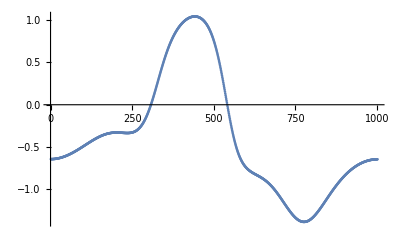

```mathematica
ListPlot[qθ1]
```

```mathematica
qθ2=Table[Qv[[ii]][[2]],{ii,1,leninvdyn}];
```

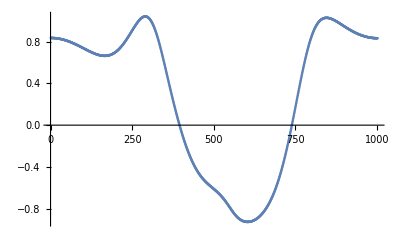

```mathematica
ListPlot[qθ2]
```

```mathematica
qθ3=Table[Qv[[ii]][[3]],{ii,1,leninvdyn}];
```

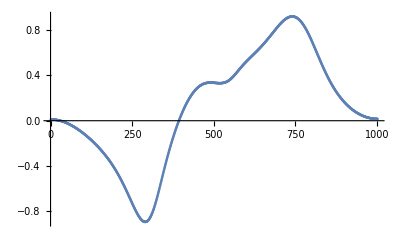

```mathematica
ListPlot[qθ3]
```

## PD Control

```mathematica
IK[{l,r,a,b,θ1,θ2,θ3,ϕ1,ϕ2,ϕ3,x,y,α}];
```

```mathematica
(* desired position velocity and acceleration*)
jointposcontrol=(IK[{l,r,a,b,θ1,θ2,θ3,ϕ1,ϕ2,ϕ3,x,y,α}]/.{x->pos[[1]],y->pos[[2]],α->pos[[3]]});
jointpos={θ1,θ2,θ3}/.jointposcontrol;
jointvel=D[jointpos,t];
jointacc=D[jointvel,t];
jpc={θ1[t]->jointpos[[1]],θ2[t]->jointpos[[2]],θ3[t]->jointpos[[3]]};
jvc={θ1'[t]->jointvel[[1]],θ2'[t]->jointvel[[2]],θ3'[t]->jointvel[[3]]};
jacc={θ1''[t]->jointacc[[1]],θ2''[t]->jointacc[[2]],θ3''[t]->jointacc[[3]]};
```

```mathematica
Mθ=Transpose[Jqθ].M.Jqθ;
```

```mathematica
Cθ=Transpose[Jqθ].M.dJqθ;
```

```mathematica
Gθ=Transpose[Jqθ].G;
```